```mathematica
ClearAll
```

ClearAll

```mathematica
<<GraphAlgorithms`
```

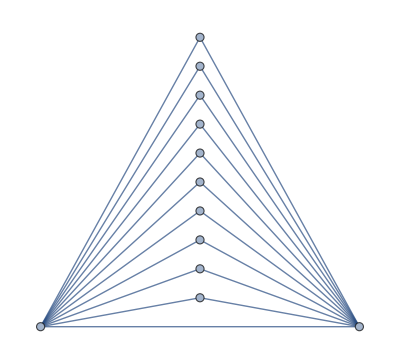

```mathematica
NestedTriangleGraph[10]
```

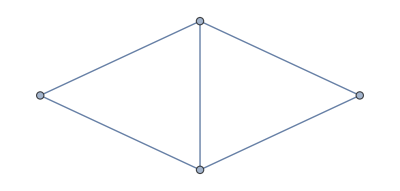

```mathematica
Graph[{1<->2, 2<->3, 1<->3, 2<->4, 1<->4}]
```

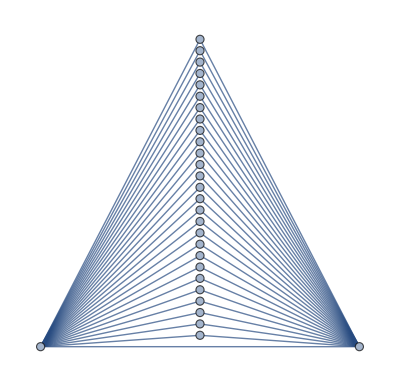

```mathematica
n=27;
Graph[Prepend[Flatten[Outer[{#1<->#2}&, {1,2}, Range[3,n+2]]], 1<->2], VertexCoordinates->Join[{{0.,0.}, {1.,0.}},Transpose[{ConstantArray[0.5, n],N[Rest[Most[Subdivide[n+1]]]]}]]]
```

```mathematica
N[Rest[Most[Subdivide[4]]]]
```

{0.25,0.5,0.75}